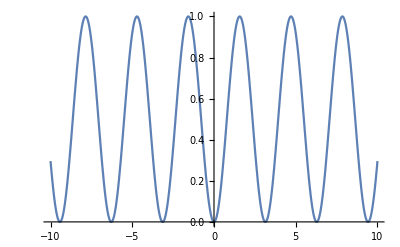

```mathematica
Plot[Sin[x]^2, {x, -10, 10}]
```

```mathematica
f[x_] := Sin[x]^2/Sqrt[x]
l[x_] := Sin[x]^2
m[x_] := 1/Sqrt[x]
n[x_] := Sqrt[x]
ListOfFunctions = {f[x], l[x], m[x], n[x]}
Integrate[ListOfFunctions, x]
```

{Sin[x]^2/(√x),Sin[x]^2,1/(√x),√x}

{√x-1/2 √π FresnelC[(2 √x)/(√π)],x/2-1/4 Sin[2 x],2 √x,(2 x^(3/2))/3}

```mathematica
Plot[{ListOfFunctions, -1/Sqrt[x]},{x,0,Pi*Pi+1},PlotLegends->"Expressions",PlotLabels->"Expressions", Filling->{2->{{3}, {LightBlue, LightRed}}}, PlotRange->{{0, Pi*Pi+1},{-2, 2}}, AxesLabel->{"x", "f(x)"}, Frame->True]
```

-Graphics-

```mathematica
Integrate[f[x], x]
```

√x-1/2 √π FresnelC[(2 √x)/(√π)]

```mathematica
g[x_] = E^(-x^2)
```

ⅇ^(-x^2)

```mathematica
g[0]+4g[.5]+2g[1]+4g[1.5]+2g[2]+4g[2.5]+2g[3]+4g[3.5]+g[4]
```

5.31718

```mathematica
NumberForm[5.317178079811257,16]
```

5.317178079811257

```mathematica
Out[13] * 4 / 24
```

0.886196

```mathematica
NumberForm[0.8861963466352095,16]
```

0.88619634663521

```mathematica
Integrate[g[x], {x, 0, Infinity}]
```

(√π)/2

```mathematica
N[(√π)/2]
```

0.886227

```mathematica
Integrate[g[x], {x, 0, 4}]
```

1/2 √π Erf[4]

```mathematica
N[1/2 √π Erf[4]]
```

0.886227

```mathematica
Integrate[1/Sqrt[x], {x, 0, 1}]
```

2

```mathematica
Integrate[f[x], {x, 0, Pi}]
```

-1/2 √π (-2+FresnelC[2])

```mathematica
N[-1/2 √π (-2+FresnelC[2])]
```

1.33975

```mathematica
2 Sqrt[Pi]
```

2 √π

```mathematica
N[2 √π]
```

3.54491

```mathematica
a = 3
b = x
c = x^2
d = Sqrt[x]
listFunctions = {a, b, c, d}
```

3

x

x^2

√x

{3,x,x^2,√x}

```mathematica
Plot[listFunctions, {x, 0, 5}, LabelStyle->Automatic, PlotLabels->{"I hate you", "2", "3", "4"}, AxesLabel->{"x", "f(x)"}, PlotRange->All]
```

-Graphics-